# Интерполационен полином на Лагранж

## Генериране на данни

```mathematica
xt = Table[5+i*0.15,{i,-3,9}]
```

{4.55,4.7,4.85,5.,5.15,5.3,5.45,5.6,5.75,5.9,6.05,6.2,6.35}

```mathematica
n = Length[xt]
```

13

```mathematica
f[x_]:=23 Cos[x^2-1]
yt = f[xt]
```

{15.1287,-14.2763,-19.8288,9.75612,21.275,-8.66902,-20.9238,11.3257,18.3575,-16.8677,-11.5441,22.2322,-1.20905}

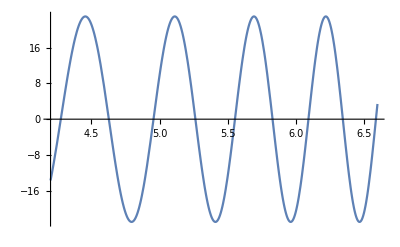

```mathematica
grf = Plot[f[x],{x,4.2,6.6}]
```

```mathematica
points =Table[{xt[[i]], yt[[i]]},{i,1,n}]
```

{{4.55,15.1287},{4.7,-14.2763},{4.85,-19.8288},{5.,9.75612},{5.15,21.275},{5.3,-8.66902},{5.45,-20.9238},{5.6,11.3257},{5.75,18.3575},{5.9,-16.8677},{6.05,-11.5441},{6.2,22.2322},{6.35,-1.20905}}

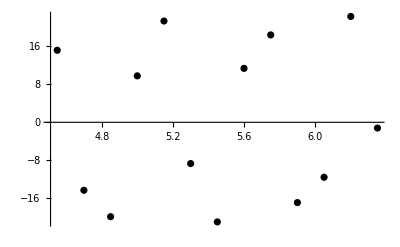

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

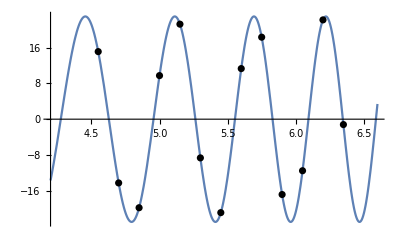

```mathematica
Show[grf,grp]
```

## Линейна интерполация

```mathematica
L1[x_]:=21.275*(x-5.3)/(5.15-5.3)-8.66902*(x-5.15)/(5.3-5.15)
```

### Проверка на интерполационните условия

```mathematica
L1[5.15]
L1[5.3]
```

21.275

-8.66902

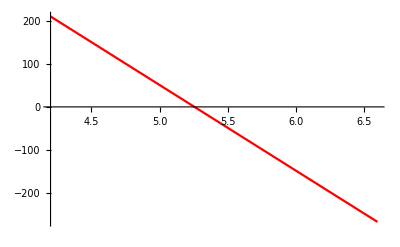

```mathematica
grL1 = Plot[L1[x],{x, 4.2,6.6}, PlotStyle->Red]
```

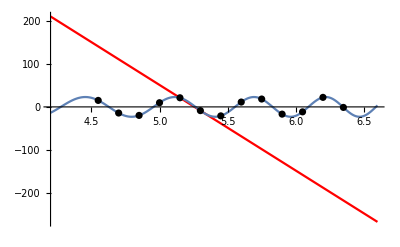

```mathematica
Show[grL1,grf,grp]
```

### Намиране на приближена стойност в т. s = 5.21

```mathematica
L1[5.21]
```

9.29739

### Оценка на грешката

#### Теоретична грешка

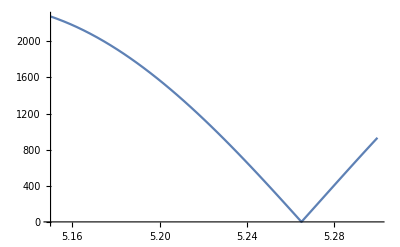

```mathematica
Plot[Abs[f''[x]],{x,5.15,5.3}]
```

```mathematica
M2 = Abs[f''[5.15]]
```

2274.54

```mathematica
R1[x_]:=M2/(2!)Abs[(x-5.15)(x -5.3)]
```

```mathematica
R1[5.21]
```

6.14127

#### Истинската грешка - за сравнение

```mathematica
Abs[L1[5.21]-f[5.21]]
```

2.90893

## Квадратична интерполация

```mathematica
L2[x_]:=9.756* ((x-5.15)(x-5.3))/((5-5.15)(5-5.3)) +                                          21.275*((x-5)(x-5.3))/((5.15-5)(5.15-5.3))-8.66902*((x-5)(x-5.15))/((5.3-5)(5.3-5.15))
```

```mathematica
Expand[L2[x]]
```

-24100.3+9429.01 x-921.4 x^2

### Проверка на интерполационните условия

```mathematica
L2[5.]
L2[5.15]
L2[5.3]
```

9.756

21.275

-8.66902

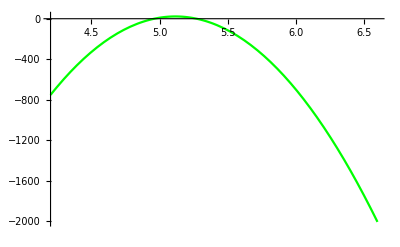

```mathematica
grL2 = Plot[L2[x],{x, 4.2,6.6}, PlotStyle->Green]
```

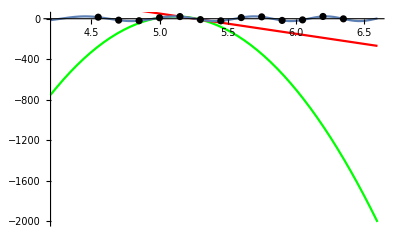

```mathematica
Show[grL2,grL1,grf,grp]
```

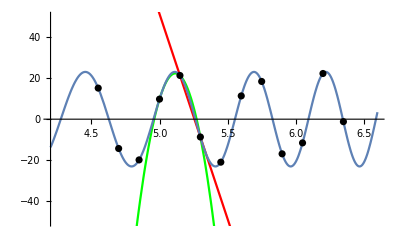

```mathematica
Show[grL2,grL1,grf,grp, PlotRange->{-50,50}]
```

### Намиране на приближена стойност в т. s = 5.21

```mathematica
L2[5.21]
```

14.273

### Оценка на грешката

#### Теоретична грешка

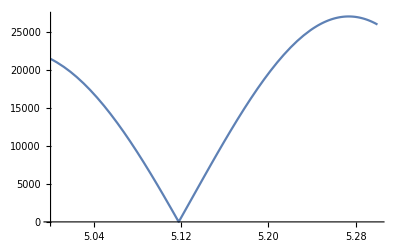

```mathematica
Plot[Abs[f'''[x]],{x,5.,5.3}]
```

```mathematica
M3 = 30000
```

30000

```mathematica
R2[x_]:=M3/(3!)Abs[(x-5)(x-5.15)(x -5.3)]
```

```mathematica
R2[5.21]
```

5.67

#### Истинската грешка - за сравнение

```mathematica
Abs[L2[5.21]-f[5.21]]
```

2.06663

## При екстраполация

### линейна интерполация

```mathematica
L1[12]
```

-1346.17

```mathematica
f[12.]
```

1.32256

```mathematica
R1[12]
```

52195.1

### квадратична интерполация

```mathematica
L2[12]
```

-43633.8

```mathematica
f[12.]
```

1.32256

```mathematica
R2[12]
```

1.60633×10^6